### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[6355450520]
```

<|Index→6355450520,QCode→34342332242423,RuleSet→{ABB→AAA,A→B,B→AA}|>

We generate the sessie and its causal network, again giving it a convenient name:

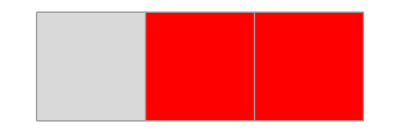

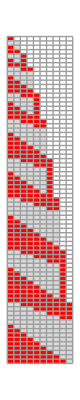
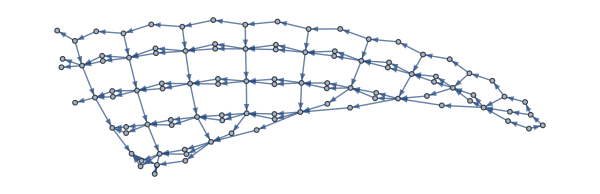
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,1→3,2→4,4→5,4→6,5→7,7→8,6→8,3→8,7→9,8→10,«604»,375→397,397→398,376→398,377→398,398→399,378→399,379→399,399→400,380→400,381→400}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1,2},{2},{5},{1,2},{2},{2},{1,2},{2,3,4},{4},{4},{3},{9},{1,2},{2,3,4},{4},{4},{3},{3},{1,3},{1,3,4},{4,5,6},{6},{6},{5},{5},{4},{13},{1,3},{1,3,4},{4,5,6},{6},{6},{5},{5},{4},{4},{1,4},{1,4,5},{1,5,6},{6,7,8},{8},{8},{7},{7},{6},{6},{5},{17},{1,4},{1,4,5},{1,5,6},{6,7,8},{8},{8},{7},{7},{6},{6},{5},{5},{1,5},{1,5,6},{1,6,7},{1,7,8},{8,9,10},{10},{10},{9},{9},{8},{8},{7},{7},{6},{21},{1,5},{1,5,6},{1,6,7},{1,7,8},{8,9,10},{10},{10},{9},{9},{8},{8},{7},{7},{6},{6},{1,6},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{10,11,12},{12},{12},{11},{11},{10},{10},{9},{9},{8},{8},{7},{25},{1,6},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{10,11,12},{12},{12},{11},{11},{10},{10},{9},{9},{8},{8},{7},{7},{1,7},{1,7,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{12,13,14},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{9},{8},{29},{1,7},{1,7,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{12,13,14},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{9},{8},{8},{1,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{14,15,16},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{33},{1,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{14,15,16},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{9},{1,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{16,17,18},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{37},{1,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{16,17,18},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{1,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{18,19,20},{20},{20},{19},{19},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{41},{1,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{18,19,20},{20},{20},{19},{19},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{1,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{20,21,22},{22},{22},{21},{21},{20},{20},{19},{19},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{},{1,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{20,21,22},{22},{22},{21},{21},{20},{20},{19},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,{20,21,22}]
```

{{341},{374}}

```mathematica
nds[[1;;374]]
```

{{1,2},{2},{5},{1,2},{2},{2},{1,2},{2,3,4},{4},{4},{3},{9},{1,2},{2,3,4},{4},{4},{3},{3},{1,3},{1,3,4},{4,5,6},{6},{6},{5},{5},{4},{13},{1,3},{1,3,4},{4,5,6},{6},{6},{5},{5},{4},{4},{1,4},{1,4,5},{1,5,6},{6,7,8},{8},{8},{7},{7},{6},{6},{5},{17},{1,4},{1,4,5},{1,5,6},{6,7,8},{8},{8},{7},{7},{6},{6},{5},{5},{1,5},{1,5,6},{1,6,7},{1,7,8},{8,9,10},{10},{10},{9},{9},{8},{8},{7},{7},{6},{21},{1,5},{1,5,6},{1,6,7},{1,7,8},{8,9,10},{10},{10},{9},{9},{8},{8},{7},{7},{6},{6},{1,6},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{10,11,12},{12},{12},{11},{11},{10},{10},{9},{9},{8},{8},{7},{25},{1,6},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{10,11,12},{12},{12},{11},{11},{10},{10},{9},{9},{8},{8},{7},{7},{1,7},{1,7,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{12,13,14},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{9},{8},{29},{1,7},{1,7,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{12,13,14},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{9},{8},{8},{1,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{14,15,16},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{33},{1,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{14,15,16},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{9},{9},{1,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{16,17,18},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{37},{1,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{16,17,18},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{10},{10},{1,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{18,19,20},{20},{20},{19},{19},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{41},{1,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{18,19,20},{20},{20},{19},{19},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{12},{11},{11},{1,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{20,21,22},{22},{22},{21},{21},{20},{20},{19},{19},{18},{18},{17},{17},{16},{16},{15},{15},{14},{14},{13},{13},{12},{},{1,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{20,21,22}}

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;374]]]
```

{{1,2},€_(n$1⊨1)^2[{2+3 (-1+n$1)}],{1,2},€^2[{2}],{1,2},{2,3,4},€^2[{4}],€_(n$3⊨1)^3[€_(n$1⊨1)^2[{3-3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-2+n$2+3 n$3},€_(n$1⊨1)^(-4+n$2+3 n$3)[{1,-3+n$1+n$2+3 n$3,-2+n$1+n$2+3 n$3}],{-6+2 n$2+6 n$3,-5+2 n$2+6 n$3,-4+2 n$2+6 n$3},€_(n$1⊨1)^(-1+3 n$3)[€^2[{-3-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-1+n$2+3 n$3},€_(n$1⊨1)^(-3+n$2+3 n$3)[{1,-2+n$1+n$2+3 n$3,-1+n$1+n$2+3 n$3}],{-4+2 n$2+6 n$3,-3+2 n$2+6 n$3,-2+2 n$2+6 n$3},€_(n$1⊨1)^(3 n$3)[€^2[{-1-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{-1+3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,n$2+3 n$3},€_(n$1⊨1)^(-2+n$2+3 n$3)[{1,-1+n$1+n$2+3 n$3,n$1+n$2+3 n$3}],{-2+2 n$2+6 n$3,-1+2 n$2+6 n$3,2 n$2+6 n$3},€_(n$1⊨1)^(1+3 n$3)[€^2[{1-n$1+2 n$2+6 n$3}]]]],{12},{},{1,11},€_(n$1⊨1)^9[{1,10+n$1,11+n$1}],{20,21,22}}

Most compressed part:

```mathematica
rsl[[8]]
```

€_(n$3⊨1)^3[€_(n$1⊨1)^2[{3-3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-2+n$2+3 n$3},€_(n$1⊨1)^(-4+n$2+3 n$3)[{1,-3+n$1+n$2+3 n$3,-2+n$1+n$2+3 n$3}],{-6+2 n$2+6 n$3,-5+2 n$2+6 n$3,-4+2 n$2+6 n$3},€_(n$1⊨1)^(-1+3 n$3)[€^2[{-3-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-1+n$2+3 n$3},€_(n$1⊨1)^(-3+n$2+3 n$3)[{1,-2+n$1+n$2+3 n$3,-1+n$1+n$2+3 n$3}],{-4+2 n$2+6 n$3,-3+2 n$2+6 n$3,-2+2 n$2+6 n$3},€_(n$1⊨1)^(3 n$3)[€^2[{-1-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{-1+3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,n$2+3 n$3},€_(n$1⊨1)^(-2+n$2+3 n$3)[{1,-1+n$1+n$2+3 n$3,n$1+n$2+3 n$3}],{-2+2 n$2+6 n$3,-1+2 n$2+6 n$3,2 n$2+6 n$3},€_(n$1⊨1)^(1+3 n$3)[€^2[{1-n$1+2 n$2+6 n$3}]]]]

```mathematica
rsl[[8]] /. {n$1->i, n$2->j, n$3->k}
```

```mathematica
€_(k⊨1)^3[
€_(i⊨1)^2[{9 k i-3 i-6 k+3}],
€_(j⊨1)^2[{1,j+3 k-2},€_(i⊨1)^(j+3 k-4)[{1,i+j+3 k-3,i+j+3 k-2}],{2 j+6 k-6,2 j+6 k-5,2 j+6 k-4},€_(i⊨1)^(3 k-1)[€^2[{-i+2 j+6 k-3}]]],
€_(i⊨1)^2[{9 i k-6 k+1}],
€_(j⊨1)^2[{1,j+3 k-1},€_(i⊨1)^(j+3 k-3)[{1,i+j+3 k-2,i+j+3 k-1}],{2 j+6 k-4,2 j+6 k-3,2 j+6 k-2},€_(i⊨1)^(3 k)[€^2[{-i+2 j+6 k-1}]]],
€_(i⊨1)^2[{9 k i+3 i-6 k-1}],
€_(j⊨1)^2[{1,j+3 k},€_(i⊨1)^(j+3 k-2)[{1,i+j+3 k-1,i+j+3 k}],{2 j+6 k-2,2 j+6 k-1,2 j+6 k},€_(i⊨1)^(3 k+1)[€^2[{-i+2 j+6 k+1}]]]]
```

```mathematica
rsl[[8]] /. {n$1->i, n$2->j, n$3->k}//InputForm
```

IndexedConcatenate[IndexedConcatenate[{3 - 3*i - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, -2 + j + 3*k}, 
  IndexedConcatenate[{1, -3 + i + j + 3*k, -2 + i + j + 3*k}, {i, 1, -4 + j + 3*k}], {-6 + 2*j + 6*k, -5 + 2*j + 6*k, -4 + 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{-3 - i + 2*j + 6*k}, 2], {i, 1, -1 + 3*k}], {j, 1, 2}], 
 IndexedConcatenate[{1 - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, -1 + j + 3*k}, 
  IndexedConcatenate[{1, -2 + i + j + 3*k, -1 + i + j + 3*k}, {i, 1, -3 + j + 3*k}], {-4 + 2*j + 6*k, -3 + 2*j + 6*k, -2 + 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{-1 - i + 2*j + 6*k}, 2], {i, 1, 3*k}], {j, 1, 2}], 
 IndexedConcatenate[{-1 + 3*i - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, j + 3*k}, 
  IndexedConcatenate[{1, -1 + i + j + 3*k, i + j + 3*k}, {i, 1, -2 + j + 3*k}], {-2 + 2*j + 6*k, -1 + 2*j + 6*k, 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{1 - i + 2*j + 6*k}, 2], {i, 1, 1 + 3*k}], {j, 1, 2}], {k, 1, 3}]

Can we do better?

```mathematica
{ExpandAll[%]}
```

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```